```mathematica
acoeff[n_]:=2/Pi*Integrate[(1-Cos[x])*Sin[n*x],{x,0,Pi}];
```

```mathematica
acoeff[1]
```

4/π

```mathematica
acoeff[n]
```

(2 (-1+Cos[n π]-2 n^2 Cos[n π]))/((-n+n^3) π)

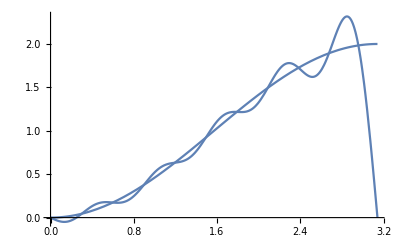

```mathematica
nterms=10;
Show[Plot[4/Pi*Sin[x]+Sum[acoeff[n]*Sin[n*x],{n,2,nterms}],{x,0,Pi}],Plot[1-Cos[x],{x,0,Pi}]]
```

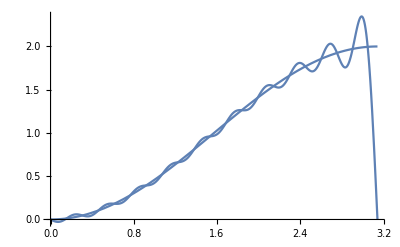

```mathematica
nterms=20;
Show[Plot[4/Pi*Sin[x]+Sum[(2*(-1)^n-4*n^2*(-1)^n-2)/(Pi*(n^3-n))*Sin[n*x],{n,2,nterms}],{x,0,Pi}],Plot[1-Cos[x],{x,0,Pi}]]
```

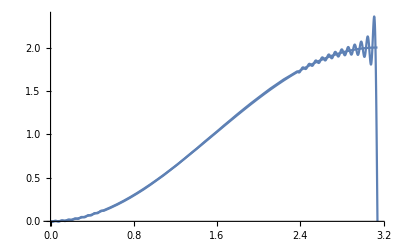

```mathematica
nterms=100;
Show[Plot[4/Pi*Sin[x]+Sum[(2*(-1)^n-4*n^2*(-1)^n-2)/(Pi*(n^3-n))*Sin[n*x],{n,2,nterms}],{x,0,Pi}],Plot[1-Cos[x],{x,0,Pi}]]
```